#### Pupal wing size measurements, hours APF

```mathematica
timesAPF = {0, 2, 4, 6};
areaKOp = {1.766,1.865,1.832,3.509};
areaKOKO = {1.767, 1.683, 2.368,4.843};
volumeKOp = {3.207,4.072,4.591,5.632};
volumeKOKO = {3.096,3.675,5.262,5.99575};
leg = {"wild-type", "dilp8 mutant"};
axArea = {"hours APF", "area 10^5μm^2"};
axVolume = {"hours APF", "volume 10^6μm^3"};
areas = {Transpose[{timesAPF, areaKOp}], Transpose[{timesAPF, areaKOKO}]};
volumes = {Transpose[{timesAPF, volumeKOp}], Transpose[{timesAPF, volumeKOKO}]};
volAreaConversion = 2;
```

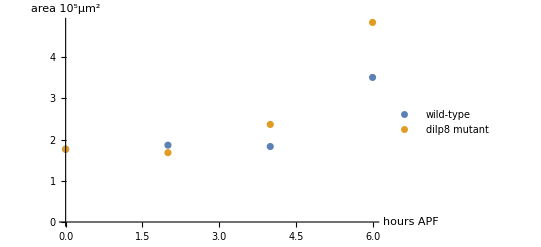

```mathematica
ListPlot[areas, PlotLegends->leg, AxesLabel->axArea]
```

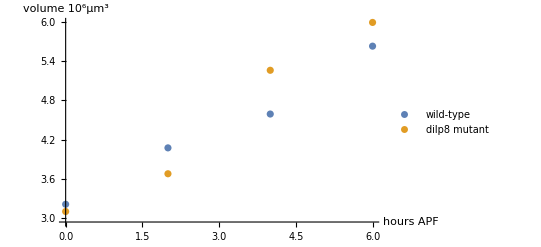

```mathematica
ListPlot[volumes, PlotLegends->leg, AxesLabel->axVolume]
```

#### FA and pupal wing size measurements, before and after pupariation

```mathematica
times = {"96hr AED","114hr AED", "7hr APF"};
volumeKOKO2 ={1.6491,1.9785,6.1033};
volumeKOp2 ={1.6444, 2.2344,5.9296};
```

Volume measurements *(10^6) μm^3

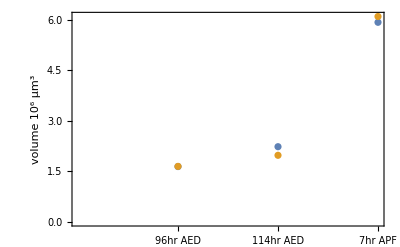

```mathematica
ListPlot[{volumeKOp2, volumeKOKO2},Frame->True,FrameTicks->{{Automatic,None},{{{1,times[[1]]},{2,times[[2]]},{3,times[[3]]}},None}}, AxesLabel->{None, "volume 10^6 μm^3"}]
```

Estimated area measurements *(10^5) μm^2

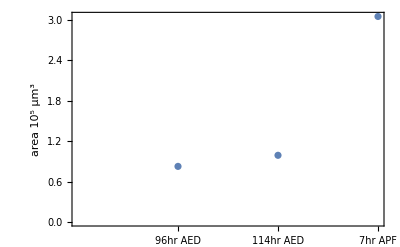

```mathematica
ListPlot[volumeKOKO2/volAreaConversion,Frame->True,FrameTicks->{{Automatic,None},{{{1,times[[1]]},{2,times[[2]]},{3,times[[3]]}},None}}, AxesLabel->{None, "area 10^5 μm^3"}]
```

```mathematica
bittigFinal = 1.5(* at t=120 hours past hatching*)
```

```mathematica
aegerterFinal = 0.8
```